# -Graphics-

# Building Custom Neural Networks

## In Wolfram Language

## Outline

Uses of AI

Definition of a neural network

Building a neural network

Do you need to build a neural network?

Building your own neural network

Do you need to build a neural network?

Pre-built networks

Getting the best model

Summary

Next steps

## Uses of AI: Quick Examples

### Classification

#### Facial emotions

Identify the emotion in a person’s face:

```mathematica
With[
{faces = {-Graphics-,-Graphics-}},
Dataset[FacialFeatures[faces]]
]
```

```mathematica
FacialFeatures[CurrentImage[]]//Dataset
```

#### Text summary

Get a summary of a piece of text:

#### Image location

### Prediction

#### Image colorization

Get an image-colouring function from the Wolfram Function Repository and apply it to a greyscale image:

```mathematica
ResourceFunction["ImageColorize"][-Graphics-]
```

### Sequence Prediction

#### Next word

Get a language modelling net from the Wolfram Neural Net Repository:

```mathematica
languageNet=NetModel[{"GPT Transformer Trained on BookCorpus Data","Task"->"LanguageModeling"}];
```

Use the net to predict the next word in a sentence:

```mathematica
languageNet["She got out of the"]
```

Use an LLM instead (requires an OpenAI API key):

```mathematica
LLMSynthesize["She got out of the "]
```

### Feature Extraction

#### Similar words

Get a word vector net from the Wolfram Neural Net Repository:

```mathematica
net=NetModel["GloVe 100-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data"];
```

Get the features of a particular word:

```mathematica
net["king"]
```

Extract the words and their associated vectors from the model:

```mathematica
wordsToVectors=AssociationThread[Normal[NetExtract[net,"Input"]]["Tokens"]->Most[Normal[NetExtract[net,"Weights"]]]];
```

Use the vectors to “navigate” the feature space, finding words close to “king” and “woman”, but not so close to “man”:

```mathematica
Nearest[wordsToVectors, wordsToVectors["king"]+wordsToVectors["woman"]-wordsToVectors["man"],5]
```

### Synthesis

#### Image restyling

Repaint an image in the styles of different artists:

```mathematica
daVinci = -Graphics-; kandinsky = -Graphics-; monet = -Graphics-; gogh = -Graphics-;
```

```mathematica
ImageRestyle[CurrentImage[],#]&/@{daVinci, kandinsky, monet, gogh}
```

### Anomaly Detection

#### Anomalous images

Find anomalous images with a custom anomaly detector:

```mathematica
mnistData =RandomSample[ResourceData["MNIST","TrainingData"][[All,1]],1000];

detectorFunction=AnomalyDetection[mnistData,Method->"Multinormal"]
```

```mathematica
FindAnomalies[detectorFunction,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

## Neural Networks

### What Is a Neural Network?

Base model with lots of parameters

Training → fine-tuning of parameter values

### Examples

Feedforward network—simple classification, facial recognition, computer vision

Convolutional—image processing, computer vision

Long short-term memory—handwriting recognition, speech recognition, machine translation

Sequence-to-sequence—image captioning, chatbots, text summarisation

Transformer—natural language processing, computer vision

## Building a Neural Network

### The Development Pipeline

#### Training

Get some data

Represent it in vector form (encoding)

Set up a model (relevant to the data type and the context)

Train the model on the data

#### Testing

Get some (unseen!) testing data

Test the model on the data

#### Validation

Does it work? (Less important: why does it work?)

Get measurements from the model

## Do You Need to Build a Neural Network?

### Automated Development Pipelines

All-in-one training, testing and validation

Very quick; little machine learning knowledge required

Single-dimension-output supervised learning (Classify, Predict, SequencePredict, …)

#### Example: Titanic

Create a Titanic survival classifier (based on class, age and sex):

```mathematica
Short[titanicData=ExampleData[{"MachineLearning","Titanic"},"Data"]]
```

```mathematica
titanicClassifier=Classify[titanicData]
```

```mathematica
titanicClassifier[{"1st",50,"male"},"Probabilities"]
```

Create a Titanic age predictor (based on class, sex and survival outcome):

```mathematica
titanicPredictor=With[
{restructuredData = ReplaceAll[titanicData, HoldPattern[{class_,age_,sex_}->outcome_]:>{class,sex,outcome}->age]},
Predict[restructuredData]
]

titanicPredictor[{"1st","male","survived"}]
```

Deploy the classifier to the cloud as a web form:

```mathematica
CloudDeploy[
FormPage[
{
{"class", "Class"} -> {"1st","2nd","3rd","unknown"},
{"age", "Age"} -> <|"Interpreter" -> Restricted["Number",{0,100}], "Input" -> 30|>,
{"sex", "Sex"} -> {"male","female","unknown"}
},
Column[{
"Estimated survival probabilities:",
PieChart[
titanicClassifier[{#class,#age,#gender},"Probabilities"],

]
}]&,
AppearanceRules -> 
],
"BuildingCustomNeuralNetworks/Titanic",
Permissions -> "Public"
]
```

### Manual Pipelines

#### Customisable

More choices for model types and data types

Fine-tuning of the model

#### High-dimensional outputs

Richer outputs

More complex measures of correctness

E.g. what makes a machine-made Picasso-style painting "good"?

#### Many degrees of freedom

More knowledge required

Need a programming language to do it (or a complicated interface)

## Building Your Own Neural Network

Guide: Neural Networks

Tech Note: Neural Networks in the Wolfram Language

### Network Design

#### Architecture

Multiple layers of “fitting” with increasing abstraction

Alternating linear and nonlinear layers

Special layers to carry out certain tasks

```mathematica
With[
{imageSize = 800},
FlipView[{
Image[-Graphics-, ImageSize -> imageSize],
Image[-Graphics-, ImageSize -> imageSize]
}]
]
```

#### Layer types

```mathematica
?*Layer*
```

### Layers Are Just Trainable Models

#### Example: Linear data (y=a+b x)

##### Linear regression

Use Fit to fit a linear model to some data:

```mathematica
data={{0,3.1},{1,3.4},{2,4.2},{3,4.4},{4,4.9},{5,5}};

model = Fit[data,{1,x},x, "Function"]
```

3.15238+0.405714 #1&

```mathematica
Show[
ListPlot[data],
Plot[model[x],{x,0,5}],

]
```

Look at the squared residuals:

```mathematica
leastSquaresPlot[data, AspectRatio -> 1]
```

##### Neural network

Create and train a simple neural net to perform the same task:

```mathematica
inputOutputData=Rule@@@data (* Set up the data *)
```

{0→3.1,1→3.4,2→4.2,3→4.4,4→4.9,5→5}

```mathematica
linearNet=LinearLayer[{}] (* Set up the net *)
```

LinearLayer[…]

```mathematica
trainedNet=NetTrain[linearNet,inputOutputData] (* Train the net *)
```

LinearLayer[…]

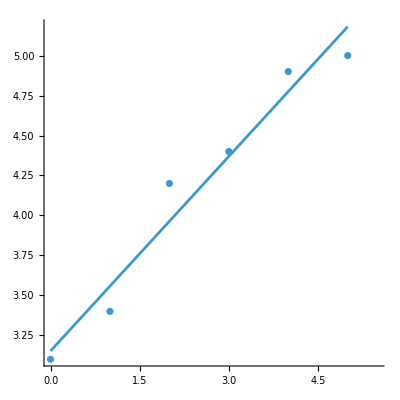

```mathematica
Show[
ListPlot[data],
Plot[trainedNet[x],{x,0,5}],

]
```

Compare the weights and biases of the net model with the coefficients of the Fit model:

```mathematica
NetExtract[trainedNet,"Weights"]//Normal
NetExtract[trainedNet,"Biases"]//Normal
```

{{0.405723}}

{3.15235}

```mathematica
CoefficientList[model[x], x]
```

{3.15238,0.405714}

### Combining Layers: NetChain

Use NetChain to feed the output of one layer into the next layer (creating a “chain” of layers).

#### Example: Simple case

Chaining layers is the same as nesting their functions:

```mathematica
NetChain[{trainedNet, trainedNet, trainedNet}]
```

NetChain[…]

```mathematica
trainedNet[ (* Third layer *)
trainedNet[ (* Second layer *)
trainedNet[ (* First layer *)
1 (* Input *)
]
]
]
```

5.01703

#### Example: Nonlinear data

Include a nonlinear layer (in this case, Ramp) to fit a model to data that has a nonlinear trend:

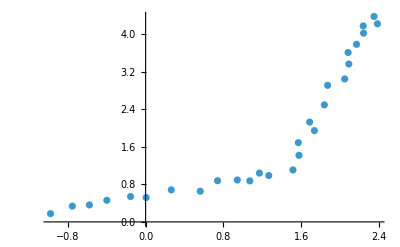

```mathematica
kinkData=;

ListPlot[kinkData]
```

```mathematica
kinkNet = NetChain[{LinearLayer[{2}],ElementwiseLayer[Ramp],LinearLayer[{1}]}];
```

```mathematica
trainedKinkNet=NetTrain[kinkNet,Rule@@@kinkData];
```

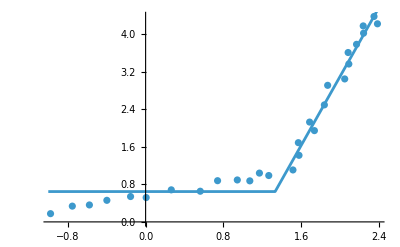

```mathematica
Show[
ListPlot[kinkData],
Plot[trainedKinkNet[x],{x,-1,5}]
]
```

#### Example: Sequence data

Attempt to learn arithmetic as sequences of strings (not a good idea!):

```mathematica
(* Set up the data: *)
Block[
{makeRule},
makeRule[a_,b_]:=IntegerString[a]<>"+"<>IntegerString[b]->a+b;
stringArithmeticTrainingData=Flatten[Table[makeRule[i,j],{i,0,99},{j,0,99}]]
];
```

```mathematica
RandomSample[stringArithmeticTrainingData,5]//InputForm
```

{"98+2" -> 100, "17+3" -> 20, "63+65" -> 128, "31+78" -> 109, "5+67" -> 72}

```mathematica
(* Create a net: *)
stringArithmeticNet=NetChain[{
UnitVectorLayer[], (* Convert a number to a one-hot vector *)
LongShortTermMemoryLayer[40], (* Learn with persistent short-term memory *)
LongShortTermMemoryLayer[20],
SequenceLastLayer[], (* Get the last output *)
LinearLayer[{}] (* Convert back to a single number *)
},
"Input"->NetEncoder[{"Characters",{DigitCharacter,"+"}}], (* Encode string inputs as numbers *)
"Output"->"Real"
];
```

```mathematica
(* Train the net: *)
trainedStringArithmeticNet=NetTrain[
stringArithmeticNet,
stringArithmeticTrainingData,
BatchSize->64,
MaxTrainingRounds->200,
ValidationSet->Scaled[0.1]
]
```

NetChain[…]

```mathematica
(* Test the net: *)
trainedStringArithmeticNet[{"5+2","10+25","9+11","44+44","100+50"}]
```

{6.61448,35.2747,19.8179,87.9528,80.9583}

### Combining Layers: NetGraph

Use NetGraph to combine layers in arbitrary ways.

#### Example: Predicting Titanic survival

Recreate the Titanic classifier:

```mathematica
titanicData=DeleteMissing[ExampleData[{"Dataset","Titanic"}],1,2]
```

```mathematica
titanicNet=NetGraph[
(* Layers: *)
{
CatenateLayer[], (* Join multiple inputs together *)
LinearLayer[],
LogisticSigmoid (* Nonlinear layer *)
},
(* Net structure: *)
{
{
NetPort["class"],
NetPort["age"],
NetPort["sex"]
}->1,
1->2->3->NetPort["survived"]
},
(* Encode the inputs: *)
"class"-> NetEncoder[{"Class",{"1st","2nd","3rd"}, "UnitVector"}], (* Encode classes as one-hot vectors *)
"age"->NetEncoder[{"Function", {#}&,{1}}],
"sex"-> NetEncoder[{"Class",{"male","female"},"UnitVector"}] (* Encode sexes as one-hot vectors *)
,
(* Decode the output: *)
"survived"->NetDecoder[{"Class",{True,False}}] (* Decode survival as a boolean (True or False) *)
]
```

NetGraph[…]

```mathematica
Magnify[Information[titanicNet, "FullSummaryGraphic"], 3] (* Network structure *)
```

```mathematica
trainedTitanicNet2= NetTrain[titanicNet,titanicData]
```

NetGraph[…]

```mathematica
With[
{
rose = <|"class"->"1st","age"->17,"sex"->"female"|>,
jack = <|"class"->"3rd","age"->20,"sex"->"male"|>
},
trainedTitanicNet/@{rose, jack}
]
```

{True,False}

### Encoders and Decoders

The type of encoder or decoder you use will depend on the data type you are training on, what you are trying to learn and the data type you would like to end up with.

#### Types

```mathematica
Grid[
{
{"Type", "Examples"},
{"Audio", Column[{"Audio","AudioMelSpectrum","AudioMFCC","AudioSpectrogram","AudioSTFT"}]},
{"Text", Column[{"SubwordTokens","Characters","Tokens","UTF8"}]},
{"Image", Column[{"Image","Image3D"}]},
{"Other", Column[{"Boolean","Class","CTCBeamSearch","Function"}]}
},
BaseStyle -> {"Text", LineIndent -> 0, TextAlignment -> Left, TextJustification -> 1},
Alignment -> {{Right, Left, Left}, Automatic, {{1, 1} -> Center, {1, 2} -> Center, {1, 3} -> Center}},
Background -> {None, {{{GrayLevel[0.95], White}}, {1 -> GrayLevel[0.88]}}},
Spacings -> {2, 1.5},
Frame -> All,
FrameStyle -> Gray
]
```

Type | Examples
Audio | Audio
AudioMelSpectrum
AudioMFCC
AudioSpectrogram
AudioSTFT
Text | SubwordTokens
Characters
Tokens
UTF8
Image | Image
Image3D
Other | Boolean
Class
CTCBeamSearch
Function

#### Example: Text encoders

```mathematica
NetEncoder["Characters"]["This is a sentence"]
```

```mathematica
NetEncoder["Tokens"]["This is a sentence"]
```

```mathematica
NetEncoder[{"SubwordTokens",File["ExampleData/sentencepiece_simple.model"]}]["supermarket"]
```

```mathematica
NetEncoder[{"SubwordTokens",File["ExampleData/sentencepiece_simple.model"]}]["superman"]
```

## Do You Need to Build a Neural Network?

### Neural Network Repository (link)

Input domains: audio, images, numbers, text, video

Task types: audio analysis, denoising, image processing, language modelling, object detection, …

#### Example: Digit recognition (LeNet)

```mathematica
leNet=NetModel["LeNet Trained on MNIST Data"]
```

```mathematica
leNet/@{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

#### Example: Depth perception

```mathematica
depthNet = NetModel["Single-Image Depth Perception Net Trained on NYU Depth V2 Data"]
```

```mathematica
randomFace = ImageResize[-Graphics-, 200]
```

```mathematica
ImageAdjust[Image[depthNet[randomFace]]]
```

## Pre-Built Networks

### Retraining Existing Networks on New Data

Existing neural networks can be retrained. Training a network with new data just optimises the weights inside the network for that particular data.

#### Example: LeNet on blurred digits

Test LeNet against data it was designed for:

```mathematica
leNetTestingData = RandomSample[ResourceData["MNIST","TestData"]];
```

```mathematica
{#, leNet[#]}&/@Keys[leNetTestingData[[;;10]]]
```

Create new data (by blurring and rotating digits):

```mathematica
newLeNetData = Map[
Rasterize[
Rotate[
Blur[
Rasterize[#],
RandomReal[{1, 5}]
],
RandomReal[{-Pi/10,  Pi/10}]
]
] -> # &,
RandomInteger[{0, 9}, 100]
];

{newLeNetTrainingData, newLeNetTestingData} = TakeDrop[newLeNetData, Floor[0.8*Length[newLeNetData]]]
```

Test the net against the new data:

```mathematica
{#, leNet[#]}&/@Keys[newLeNetTestingData]
```

Retrain the net on the new data and retest:

```mathematica
newLeNet=NetTrain[leNet, newLeNetTrainingData]
```

```mathematica
{#, newLeNet[#]}&/@Keys[newLeNetTestingData]
```

#### Example: LeNet on Eastern Arabic numerals

Test LeNet against an Eastern Arabic numeral:

```mathematica
leNet[-Graphics-]
```

Retrain the network with new data:

```mathematica
easternLeNet=NetTrain[
leNet,
{-Graphics-->6,-Graphics-->1,-Graphics-->1,-Graphics-->3,-Graphics-->2,-Graphics-->5,-Graphics-->7,-Graphics-->9,-Graphics-->1,-Graphics-->6,-Graphics-->7,-Graphics-->5,-Graphics-->1,-Graphics-->2,-Graphics-->9,-Graphics-->7,-Graphics-->8,-Graphics-->4,-Graphics-->6,-Graphics-->2,-Graphics-->8,-Graphics-->4,-Graphics-->3,-Graphics-->8,-Graphics-->8,-Graphics-->7,-Graphics-->3,-Graphics-->6,-Graphics-->6,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->9,-Graphics-->3,-Graphics-->1,-Graphics-->6,-Graphics-->7,-Graphics-->5,-Graphics-->3,-Graphics-->5,-Graphics-->1,-Graphics-->3,-Graphics-->4,-Graphics-->5,-Graphics-->8,-Graphics-->9,-Graphics-->7,-Graphics-->5,-Graphics-->9,-Graphics-->8,-Graphics-->9}
]
```

Retest:

```mathematica
easternLeNet[-Graphics-]
```

### Modifying the Purpose of a Network

#### Example: LeNet on language detection

LeNet was designed to recognise Western Arabic numerals (i.e. classify images as being one of the digits 0–9):

```mathematica
{#, leNet[#]}&/@Keys[RandomSample[ResourceData["MNIST","TestData"], 10]]
```

Change the output to a length-2 vector using NetReplacePart and modify the decoder to recognise just two classes (“Western” and “Eastern”):

```mathematica
numeralNet=NetReplacePart[
leNet,
{
10 (* Index for the final linear layer *)->LinearLayer[2],
"Output"->NetDecoder[{"Class",{"Western","Eastern"}}]
}
]
```

Get some new data and retrain the net:

```mathematica
numerals = Join[, ]
```

```mathematica
trainedNumeralNet=NetTrain[numeralNet,numerals]
```

The modified net now classifies characters as being either Western or Eastern Arabic numerals:

```mathematica
trainedNumeralNet/@{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

#### Example: ImageIdentify Net V1 on rock, paper, scissors

ImageIdentify Net V1 was designed to recognise objects in images:

```mathematica
imageNet=NetModel["Wolfram ImageIdentify Net V1"]
```

NetChain[<24>]

```mathematica
imageNet[-Graphics-]
```

Modify the net to classify the image as being rock, paper or scissors:

```mathematica
rpsNet=NetInitialize[
NetReplacePart[
imageNet,
{
"linear"->LinearLayer[3],
"Output"->NetDecoder[{"Class",{"Rock","Paper","Scissors"}}]
}
]
]
```

NetChain[<24>]

Get some new data and retrain the net:

```mathematica
rpsData = {-Graphics-->"Scissors",-Graphics-->"Paper",-Graphics-->"Rock",,-Graphics-->"Paper",-Graphics-->"Scissors",-Graphics-->"Paper"};

rpsTrained=NetTrain[
rpsNet,
rpsData,
LearningRateMultipliers->{"linear"->1,_->None}, (* Focus all learning on the new "linear" layer *)
MaxTrainingRounds->4
]
```

NetChain[<24>]

Test the net on unseen images:

```mathematica
rpsTrained/@{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

## Getting the Best Model

### Speed vs Quality

NetTrain has various options for fine-tuning the training process. There is often a tradeoff between speed of training and quality of results.

```mathematica
Grid[
{
{"Option", "Description"},
{"TimeGoal", "The number of seconds to train for"},
{"PerformanceGoal", "Favour settings with specific advantages"},
{"Method", "The training method to use"},
{"TargetDevice", "The target device on which to perform training"},
{"LossFunction", "The loss function for assessing outputs"},
{"BatchSize", "How many examples to process in a batch"},
{"MaxTrainingRounds", "How many times to traverse the training data"},
{"LearningRate", "Rate at which to adjust weights to minimise loss"}
},
BaseStyle -> {"Text", LineIndent -> 0, TextAlignment -> Left, TextJustification -> 1},
Alignment -> {{Right, Left, Left}, Automatic, {{1, 1} -> Center, {1, 2} -> Center, {1, 3} -> Center}},
Background -> {None, {{{GrayLevel[0.95], White}}, {1 -> GrayLevel[0.88]}}},
Spacings -> {2, 1.5},
Frame -> All,
FrameStyle -> Gray
]
```

Option | Description
TimeGoal | The number of seconds to train for
PerformanceGoal | Favour settings with specific advantages
Method | The training method to use
TargetDevice | The target device on which to perform training
LossFunction | The loss function for assessing outputs
BatchSize | How many examples to process in a batch
MaxTrainingRounds | How many times to traverse the training data
LearningRate | Rate at which to adjust weights to minimise loss

(There are many more options available in the NetTrain documentation.)

### Generalisation and Overfitting

A neural network that performs perfectly on a set of training data may perform poorly in general (recall LeNet applied to the blurred images):

```mathematica
dataFitter[]
```

#### Example: Too many degrees of freedom

Create some data by adding noise to an exponential curve:

```mathematica
expData=Table[x->Exp[-x^2]+RandomVariate[NormalDistribution[0,0.15]],{x,-3,3,0.2}]
```

{-3.→-0.105622,-2.8→-0.328484,-2.6→-0.17649,-2.4→-0.168606,-2.2→0.129308,-2.→0.00819757,-1.8→-0.0792397,-1.6→0.00828204,-1.4→0.0322006,-1.2→0.199346,-1.→0.533835,-0.8→0.426252,-0.6→0.770997,-0.4→0.620518,-0.2→1.21385,1.66533×10^-16→1.09475,0.2→1.13563,0.4→0.863228,0.6→1.11108,0.8→0.329802,1.→0.461841,1.2→0.261207,1.4→-0.0199958,1.6→0.0359433,1.8→0.254556,2.→-0.145,2.2→0.376776,2.4→0.0167655,2.6→-0.0106554,2.8→-0.0106507,3.→0.176579}

Plot the data:

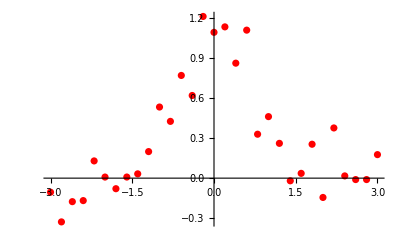

```mathematica
plot=ListPlot[List@@@expData,PlotStyle->Red]
```

Create a network with many parameters and train it on the data:

```mathematica
expNet=NetChain[{LinearLayer[150],Tanh,LinearLayer[150],Tanh,1}]
```

NetChain[…]

```mathematica
trainedExpNet=NetTrain[expNet,expData,Method->"ADAM",TimeGoal->15];
```

The result (provided the network has been left to train for long enough) is a curve that overfits the data:

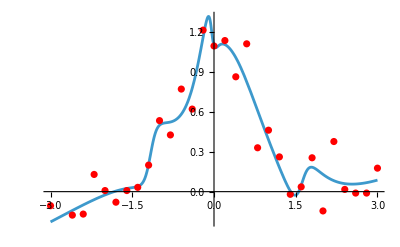

```mathematica
Show[Plot[trainedExpNet[x],{x,-3,3}],plot]
```

### Preventing Overfitting

#### Regularisation

Regularisation is a way of simplifying a network.

Regularise the network using the "L2Regularization" option. This determines how much emphasis to give global errors during the training by modifying the loss function:

```mathematica
trainedRegNet=NetTrain[expNet,expData,Method->{"ADAM","L2Regularization"->0.01},TimeGoal->15]
```

```mathematica
Show[Plot[trainedRegNet[x],{x,-3,3}],plot]
```

#### Dilution

Dilution is a regularisation technique that “thins out” the input data by randomly setting elements to zero (i.e. “dropping” them).

Dilute the network by inserting a dropout layer:

```mathematica
trainedDropNet=NetTrain[NetInsert[expNet,DropoutLayer[0.8],3],expData,Method->"ADAM",TimeGoal->10];
```

```mathematica
Show[Plot[trainedDropNet[x],{x,-3,3}],plot]
```

#### Validation

Validation is a way of testing and checking (i.e. validating) a network as it is trained.

Validate the network by using a validation set:

```mathematica
validationData=Table[x->Exp[-x^2]+RandomVariate[NormalDistribution[0,0.15]],{x,-3,3,0.2}];
```

```mathematica
trainedValNet=NetTrain[expNet,expData,Method->"ADAM",TimeGoal->10,ValidationSet->validationData]
```

```mathematica
Show[Plot[trainedValNet[x],{x,-3,3}],plot]
```

### Validation

#### Example: LeNet

```mathematica
leNet=NetModel["LeNet Trained on MNIST Data"];
leNetTestingData = ResourceData["MNIST","TestData"];
```

```mathematica
NetMeasurements[leNet,leNetTestingData,"Accuracy"]
```

```mathematica
NetMeasurements[leNet,leNetTestingData,"ConfusionMatrixPlot"]//Magnify
```

```mathematica
GraphicsRow[
{
BarChart[NetMeasurements[leNet,leNetTestingData,"FalsePositiveRate"],],
BarChart[NetMeasurements[leNet,leNetTestingData,"FalseNegativeRate"],]
},
ImageSize -> 800
]
```

#### Example: Titanic

```mathematica
With[
{data = DeleteMissing[ExampleData[{"Dataset","Titanic"}],1,2]},
{titanicTrainingData, titanicTestingData}=TakeDrop[data,Floor[0.8*Length[data]]]
];
```

```mathematica
trainedTitanicNet=NetTrain[titanicNet (* NetGraph created earlier *), titanicTrainingData]
```

```mathematica
NetMeasurements[trainedTitanicNet,titanicTestingData,"Accuracy"]
```

```mathematica
NetMeasurements[trainedTitanicNet,titanicTestingData,"ConfusionMatrixPlot"]//Magnify
```

## Summary

Symbolic representation enables high-level specification

Automation can take care of the details

Neural networks require lots of data

## Next Steps

#### Become a Wolfram Language User

https://wolfram.com/mathematica/trial
https://wolframcloud.com

#### Learn Wolfram Language

https://wolfram.com/wolfram-u/an-elementary-introduction-to-the-wolfram-language

#### Subscribe to Wolfram Notebook Assistant + LLM Kit

https://www.wolfram.com/notebook-assistant-llm-kit/

#### Join the Study Group

https://www.wolfram.com/wolfram-u/special-event/study-groups/

#### Learn More Advanced Wolfram Neural Networks

https://reference.wolfram.com/language/tutorial/NeuralNetworksOverview.html

## Additional Resources

The Wolfram Documentation Center provides in-depth information on Wolfram Language functions and programming advice. Additionally, https://www.wolfram.com/mathematica/resources provides a range of videos and other resources focused on the specific capabilities of the language. 
For interesting examples of what can be achieved with the language, check out blog.wolfram.com.

Some other useful links:

Wolfram Community (a place to ask questions)

Wolfram|Alpha (a computational knowledge engine)

Wolfram Language Demonstrations (example code for all domains)

Latest Features in Mathematica 14, 14.1, and 14.2

## Thank you for listening!

Writing High-Performance Code
Tuesday, June 30, 2026 3:00 PM BST
Registration link: https://wolfr.am/1FfvGRzfq

## -Graphics-

### Initialisation

```mathematica
ClearAll[dataFitter];
dataFitter[] := (
SeedRandom[1];
With[
{
dataLength = 21,
imageSize = {500, 400}
},
With[
{
data = Table[{x, (5+x) (2+(-2/3+x/12) (3+x))+RandomReal[{0, 5}]}, {x, -Floor[dataLength/2], Ceiling[dataLength/2]}]
},
DynamicModule[
{
plot, bestFit, n = 1, showFit = True, locs = dataLength*{{-0.25,-0.25}, {0.25, 0.25}}, fitType = "Manual"
},
plot = ListPlot[
data,
Axes -> False,
Frame -> True,
FrameLabel -> {Style["x", "TI", 12, Bold], Style["y", "TI", 12, Bold]},
ImageSize -> imageSize,
PlotStyle -> GrayLevel[0.2],
PlotHighlighting -> None
];
DynamicWrapper[
Column[
{
Grid[
{
{"Degree:", Row[{Slider[Dynamic[n], {1, dataLength-1, 1}, Enabled -> Dynamic[showFit]], Spacer[10], Dynamic[n]}]},
{"Fit type:", SetterBar[Dynamic[fitType], {"Manual", "Automatic"}, Enabled -> Dynamic[showFit]]},
{"Show fit:", Checkbox[Dynamic[showFit], {False, True}]},
{Button["Reset", (n = 1; showFit = True; locs = dataLength*{{-0.25,-0.25}, {0.25, 0.25}}; fitType = "Manual")], ""}
},
Alignment -> {{Right, Left}}
],
Row[
{
Dynamic@If[
showFit,
Pane[
LocatorPane[
Dynamic[locs],
Show[
plot,
Plot[
bestFit,
{x,-Floor[dataLength/2], Ceiling[dataLength/2]},
PlotRange -> Full,
PlotStyle -> If[SameQ[fitType, "Manual"], RGBColor[0, 0.34, 0.79], RGBColor[0.84, 0, 0.08]],
PlotHighlighting -> None
]
],
LocatorAutoCreate->{1, n+2},
Appearance -> If[SameQ[fitType, "Manual"], Graphics[{RGBColor[0, 0.34, 0.79], Disk[]}, ImageSize -> 10], None],
ContinuousAction -> False,
BaselinePosition->Baseline,
Enabled -> Dynamic[SameQ[fitType, "Manual"]]
],
imageSize+{7, 7},
Alignment -> {Center, Center}
],
Pane[
plot,
imageSize+{7, 7},
Alignment -> {Center, Center}
]
],
Pane[
Dynamic@Style[
If[showFit,ResourceFunction["CoefficientMap"][Round[#, 0.0001]&, bestFit],""],
If[SameQ[fitType, "Manual"], RGBColor[0, 0.34, 0.79], RGBColor[0.84, 0, 0.08]]
],
{imageSize[[1]], 80}
]
},
Spacer[30]
]
},
Alignment -> {Left, Top},
BaseStyle -> {"Text", LineIndent -> 0},
Spacings -> {2, Automatic}
],
locs = Part[locs, 1;;UpTo[n+1]];
bestFit=Quiet[LinearModelFit[If[fitType==="Manual",locs,data],x^Range[n],x]["BestFit"]]
]
]
]
]
);
```

```mathematica
ClearAll[pointToLSPolygon, leastSquaresPlot];

Options[leastSquaresPlot]=DeleteDuplicatesBy[
Join[
{
"SquareStyle"->{Opacity[0.2]},
AspectRatio -> Automatic,
PlotRange -> Full
},
Options[Plot],
Options[ListPlot]
],
First
];

pointToLSPolygon[{x_,y_},fn_,var_]:=Block[
{
sq=(fn/.var->x)-y
},
Tooltip[
Polygon[{{x,y},{x+sq,y},{x+sq,y+sq},{x,y+sq},{x,y}}],
sq^2
]
];

leastSquaresPlot[data_,opts:OptionsPattern[]]:=leastSquaresPlot[data,1,opts];

leastSquaresPlot[data_,n_Integer?Positive,opts:OptionsPattern[]]:=Block[
{x},
leastSquaresPlot[data,LinearModelFit[data,Table[x^i,{i,0,n}],x][x],x,opts]
];

leastSquaresPlot[data_,fn_,var_,opts:OptionsPattern[]]/;MatchQ[Dimensions[data],{_}]:=leastSquaresPlot[
Transpose[{Range[Length[data]],data}],
fn,
var,
opts
];

leastSquaresPlot[data_,fn_,var_,opts:OptionsPattern[]]/;MatchQ[Dimensions[data],{_,2}]:=Block[
{pts,line},
(
line=Quiet[
Plot[
fn,
{var,Sequence@@First[PlotRange[pts]]},
Evaluate[
Sequence @@ FilterRules[{opts},Options[Plot]]
]
]
];
pts=ListPlot[
data,
Sequence@@FilterRules[{opts},Options[ListPlot]]
];
Show[
line,
pts,
Prolog->Flatten[{
OptionValue["SquareStyle"],
pointToLSPolygon[#,fn,var]&/@data
}],
Sequence@@FilterRules[Join[{opts},Options[leastSquaresPlot]],Options[ListPlot]]
]
)
];
```